```mathematica
Clear["Global`*"]

(* Define convenience function for Jacobian *)
JacobianMatrix[f_List?VectorQ,x_List]:=Outer[D,f,x]/;Equal@@(Dimensions/@{f,x})
```

```mathematica
dRdt=r (1-R/Κ)R -aRC R C - aRO R O
 dCdt=eRC aRC R C -  aCO C O - mC C
 dOdt=eRO aRO R O+ eCO aCO C O - mO O
```

-aRC C R-aRO O R+r R (1-R/Κ)

-C mC-aCO C O+aRC C eRC R

aCO C eCO O-mO O+aRO eRO O R

```mathematica
equil=FullSimplify[Solve[{ dRdt==0,dCdt==0,dOdt==0},{R,C,O}]];
equil//TableForm
```

R→Κ | C→0 | O→0
R→mO/(aRO eRO) | C→0 | O→(r (-mO+aRO eRO Κ))/(aRO^2 eRO Κ)
R→mC/(aRC eRC) | C→(r (-mC+aRC eRC Κ))/(aRC^2 eRC Κ) | O→0
R→0 | C→mO/(aCO eCO) | O→-mC/aCO
R→0 | C→0 | O→0
R→((aRO eCO mC-aRC mO+aCO eCO r) Κ)/(aCO eCO r+aRC aRO (eCO eRC-eRO) Κ) | C→(aCO mO r-aRO (aRO eRO mC-aRC eRC mO+aCO eRO r) Κ)/(aCO (aCO eCO r+aRC aRO (eCO eRC-eRO) Κ)) | O→(-aCO eCO mC r+aRC (aRO eRO mC-aRC eRC mO+aCO eCO eRC r) Κ)/(aCO (aCO eCO r+aRC aRO (eCO eRC-eRO) Κ))

```mathematica
(* Parameter sets from Diehl & Feissel 2000 *)
parms={Κ->3,r-> 0.4,aRC->0.1,aRO-> 0.1,aCO->0.05,eRC->0.8,eRO-> 0.2,eCO->0.5,mC->0.06,mO->0.04};
```

```mathematica
(* Focal equilibria *)
TableForm[equil/.parms]
```

R→3 | C→0 | O→0
R→2. | C→0 | O→1.33333
R→0.75 | C→3. | O→0
R→0 | C→1.6 | O→-1.2
R→0 | C→0 | O→0
R→1.6875 | C→0.25 | O→1.5

```mathematica
(* Community matrix *)
A=JacobianMatrix[{dRdt,dCdt,dOdt},{R,C,O}]//FullSimplify;
 (* Evaluated at each equilibrium *)
Aeq1=A/.equil[[1,All]]//FullSimplify;
Aeq2=A/.equil[[2,All]]//FullSimplify;
Aeq3=A/.equil[[3,All]]//FullSimplify;
Aeq4=A/.equil[[4,All]]//FullSimplify;
Aeq5=A/.equil[[5,All]]//FullSimplify;
Aeq6=A/.equil[[6,All]]//FullSimplify;

Aeq1//MatrixForm
```

(-r | -aRC Κ | -aRO Κ
0 | -mC+aRC eRC Κ | 0
0 | 0 | -mO+aRO eRO Κ)

```mathematica
(******************************)
(* use Carrying capacity 'Κ' as control parameter *)
(******************************)
subparms=Delete[parms,1];
```

```mathematica
(* Functions for species-specific equilibria *)
pEquilR[Κ_]=equil[[All,1,2]]/.subparms//FullSimplify
pEquilC[Κ_]=equil[[All,2,2]]/.subparms//FullSimplify;
pEquilO[Κ_]=equil[[All,3,2]]/.subparms//FullSimplify;
```

{Κ,2.,0.75,0,0,(4.5 Κ)/(5.+1. Κ)}

```mathematica
(* Functions for feasible abundances *)
AllFeas1[Κ_]=AllTrue[Re[equil[[1,All,2]]/.subparms],#≥0&]
AllFeas2[Κ_]=AllTrue[Re[equil[[2,All,2]]/.subparms],#≥0&];
AllFeas3[Κ_]=AllTrue[Re[equil[[3,All,2]]/.subparms],#≥0&];
AllFeas4[Κ_]=AllTrue[Re[equil[[4,All,2]]/.subparms],#≥0&];
AllFeas5[Κ_]=AllTrue[Re[equil[[5,All,2]]/.subparms],#≥0&];
AllFeas6[Κ_]=AllTrue[Re[equil[[6,All,2]]/.subparms],#≥0&];
```

Re[Κ]≥0

```mathematica
AllFeas1[1]
```

True

```mathematica
(* Functions for dominant eigenvalues *)
pReEig1[Κ_]=Max[Re[Eigenvalues[Aeq1/.subparms]]]
pReEig2[Κ_]=Max[Re[Eigenvalues[Aeq2/.subparms]]];
pReEig3[Κ_]=Max[Re[Eigenvalues[Aeq3/.subparms]]];
pReEig4[Κ_]=Max[Re[Eigenvalues[Aeq4/.subparms]]];
pReEig5[Κ_]=Max[Re[Eigenvalues[Aeq5/.subparms]]];
pReEig6[Κ_]=Max[Re[Eigenvalues[Aeq6/.subparms]]];
```

Max[-0.4,-0.04+0.02 Re[Κ],-0.06+0.08 Re[Κ]]

```mathematica
(* Plot stable and unstable equilibria as function of carrying capacity Κ *)
Κmin=0;Κmax=5;
ymin=-0.005;
flabx=0.11;
ELineCols={
{Thick,Brown},{Thick,Dashed, Brown},
{Thick,Green},{Thick,Dashed,Green},
{Thick,Blue},{Thick,Dashed,Blue},
{Thin,Purple},{Thin,Dashed,LightPurple},
{Thin,Gray},{Thin,Dashed,LightGray},
{Thick,Red},{Thick,Dashed,Red}};
```

```mathematica
(* Intermediate consumer *)
PlotEqC1=Plot[{pEquilC[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqC1u=Plot[{pEquilC[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqC2=Plot[{pEquilC[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqC2u=Plot[{pEquilC[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqC3=Plot[{pEquilC[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqC3u=Plot[{pEquilC[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];

PlotEqC4=Plot[{pEquilC[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[7]],RegionFunction->Function[{x},pReEig4[x]<0&&AllFeas4[x]]];
PlotEqC4u=Plot[{pEquilC[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[8]],RegionFunction->Function[{x},pReEig4[x]>0&&AllFeas4[x]]];

PlotEqC5=Plot[{pEquilC[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[9]],RegionFunction->Function[{x},pReEig5[x]<0&&AllFeas5[x]]];
PlotEqC5u=Plot[{pEquilC[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[10]],RegionFunction->Function[{x},pReEig5[x]>0&&AllFeas5[x]]];

PlotEqC6=Plot[{pEquilC[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig6[x]<0&&AllFeas6[x]]];
PlotEqC6u=Plot[{pEquilC[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[12]],RegionFunction->Function[{x},pReEig6[x]>0&&AllFeas6[x]]];
```

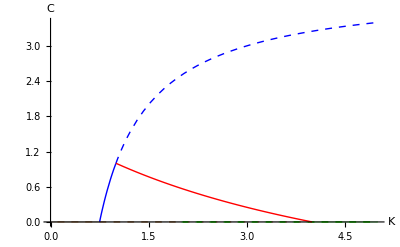

```mathematica
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u,  PlotEqC4,PlotEqC4u,  PlotEqC5,PlotEqC5u, PlotEqC6,PlotEqC6u,
PlotRange->Automatic,
AxesLabel->{"K","C"}]
```

```mathematica
(* Omnivore *)
PlotEqO1=Plot[{pEquilO[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqO1u=Plot[{pEquilO[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqO2=Plot[{pEquilO[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqO2u=Plot[{pEquilO[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqO3=Plot[{pEquilO[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqO3u=Plot[{pEquilO[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];

PlotEqO4=Plot[{pEquilO[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[7]],RegionFunction->Function[{x},pReEig4[x]<0&&AllFeas4[x]]];
PlotEqO4u=Plot[{pEquilO[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[8]],RegionFunction->Function[{x},pReEig4[x]>0&&AllFeas4[x]]];

PlotEqO5=Plot[{pEquilO[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[9]],RegionFunction->Function[{x},pReEig5[x]<0&&AllFeas5[x]]];
PlotEqO5u=Plot[{pEquilO[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[10]],RegionFunction->Function[{x},pReEig5[x]>0&&AllFeas5[x]]];

PlotEqO6=Plot[{pEquilO[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig6[x]<0&&AllFeas6[x]]];
PlotEqO6u=Plot[{pEquilO[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[12]],RegionFunction->Function[{x},pReEig6[x]>0&&AllFeas6[x]]];

 (* Basal resource *)
PlotEqR1=Plot[{pEquilR[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[1]],RegionFunction->Function[{x},pReEig1[x]<0&&AllFeas1[x]]];
PlotEqR1u=Plot[{pEquilR[Κ][[1]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[2]],RegionFunction->Function[{x},pReEig1[x]>0&&AllFeas1[x]]];

PlotEqR2=Plot[{pEquilR[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[3]],RegionFunction->Function[{x},pReEig2[x]<0&&AllFeas2[x]]];
PlotEqR2u=Plot[{pEquilR[Κ][[2]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[4]],RegionFunction->Function[{x},pReEig2[x]>0&&AllFeas2[x]]];

PlotEqR3=Plot[{pEquilR[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[5]],RegionFunction->Function[{x},pReEig3[x]<0&&AllFeas3[x]]];
PlotEqR3u=Plot[{pEquilR[Κ][[3]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[6]],RegionFunction->Function[{x},pReEig3[x]>0&&AllFeas3[x]]];

PlotEqR4=Plot[{pEquilR[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[7]],RegionFunction->Function[{x},pReEig4[x]<0&&AllFeas4[x]]];
PlotEqR4u=Plot[{pEquilR[Κ][[4]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[8]],RegionFunction->Function[{x},pReEig4[x]>0&&AllFeas4[x]]];

PlotEqR5=Plot[{pEquilR[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[9]],RegionFunction->Function[{x},pReEig5[x]<0&&AllFeas5[x]]];
PlotEqR5u=Plot[{pEquilR[Κ][[5]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[10]],RegionFunction->Function[{x},pReEig5[x]>0&&AllFeas5[x]]];

PlotEqR6=Plot[{pEquilR[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[11]],RegionFunction->Function[{x},pReEig6[x]<0&&AllFeas6[x]]];
PlotEqR6u=Plot[{pEquilR[Κ][[6]]},{Κ,Κmin,Κmax},PlotStyle->ELineCols[[12]],RegionFunction->Function[{x},pReEig6[x]>0&&AllFeas6[x]]];
```

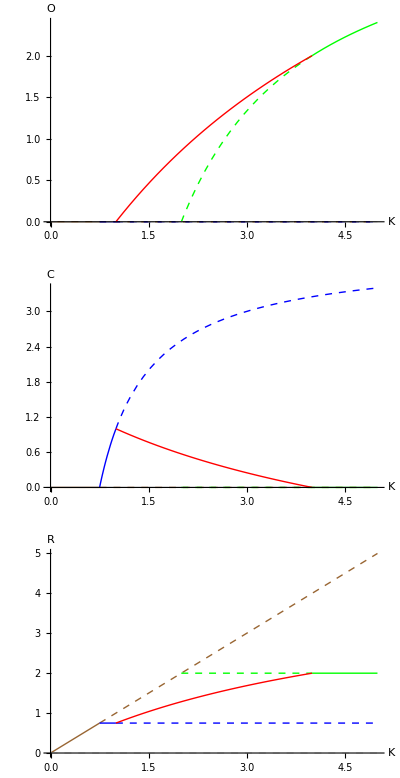

```mathematica
GraphicsGrid[{{
Show[PlotEqO1,PlotEqO1u,  PlotEqO2,PlotEqO2u,  PlotEqO3,PlotEqO3u,  PlotEqO4,PlotEqO4u,  PlotEqO5,PlotEqO5u, PlotEqO6,PlotEqO6u,PlotRange->Automatic,AxesLabel->{"K","O"}]
},{
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u,  PlotEqC4,PlotEqC4u,  PlotEqC5,PlotEqC5u, PlotEqC6,PlotEqC6u,PlotRange->Automatic,AxesLabel->{"K","C"}]
},{
Show[PlotEqR1,PlotEqR1u,  PlotEqR2,PlotEqR2u,  PlotEqR3,PlotEqR3u,  PlotEqR4,PlotEqR4u,  PlotEqR5,PlotEqR5u, PlotEqR6,PlotEqR6u,PlotRange->Automatic,AxesLabel->{"K","R"}]
}}]
```

```mathematica
(* Invasion thresholds *)
RstarCO=Solve[dCdt==0,R] //Flatten
RstarOC=Solve[dOdt==0,R]//Flatten
```

{R→(mC+aCO O)/(aRC eRC)}

{R→(-aCO C eCO+mO)/(aRO eRO)}

```mathematica
(* Invasion thresholds in absence of other consumer *)
RstarC=Solve[dCdt==0,R] /.{O->0} //Flatten
RstarO=Solve[dOdt==0,R]/.{C->0}//Flatten
```

{R→mC/(aRC eRC)}

{R→mO/(aRO eRO)}

```mathematica
(* When can top-consumer invade RC system at equilibrium? *)
RCeq=equil[[3]];
CstarO=Solve[dOdt==0,C]/.RCeq[[1]]//Flatten;
RCeqC=equil[[3,2,2]];
RCstarO=Solve[CstarO[[1,2]]-RCeq[[2,2]]==0,Κ]//FullSimplify//Flatten
```

{Κ→(aCO eCO mC r)/(aRC (aRO eRO mC-aRC eRC mO+aCO eCO eRC r))}

```mathematica
(* Does intermediate consumer abundance always decline with increasing Κ in 3-spp coexistence state ? *)
RCOeq=equil[[6]]
```

{R→((aRO eCO mC-aRC mO+aCO eCO r) Κ)/(aCO eCO r+aRC aRO (eCO eRC-eRO) Κ),C→(aCO mO r-aRO (aRO eRO mC-aRC eRC mO+aCO eRO r) Κ)/(aCO (aCO eCO r+aRC aRO (eCO eRC-eRO) Κ)),O→(-aCO eCO mC r+aRC (aRO eRO mC-aRC eRC mO+aCO eCO eRC r) Κ)/(aCO (aCO eCO r+aRC aRO (eCO eRC-eRO) Κ))}

```mathematica
(* Answer: yes - declines ∝ 1/Κ*)
derivCeqC=D[RCOeq[[2,2]],Κ]//FullSimplify
derivCeqC/.subparms
```

-(aRO eRO r (aRO eCO mC-aRC mO+aCO eCO r))/(aCO eCO r+aRC aRO (eCO eRC-eRO) Κ)^2

-0.000072/(0.01+0.002 Κ)^2

```mathematica
(* When does intermediate consumer get excluded? *)
Cex=Solve[RCOeq[[2,2]]==0,Κ]//Flatten
```

{Κ→(aCO mO r)/(aRO (aRO eRO mC-aRC eRC mO+aCO eRO r))}

```mathematica
pRstarC=ContourPlot[x=={RstarC[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,2},ContourStyle->{DotDashed,Purple}];
pRstarO=ContourPlot[x=={RstarO[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,2},ContourStyle->{DotDashed,DarkGreen}];
pRCstarO=ContourPlot[x=={RCstarO[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,2},ContourStyle->{DotDashed,Orange}];
pCex=ContourPlot[x=={Cex[[1,2]]/.parms},{x,Κmin,Κmax},{y,0,2},ContourStyle->{DotDashed,Black}];
```

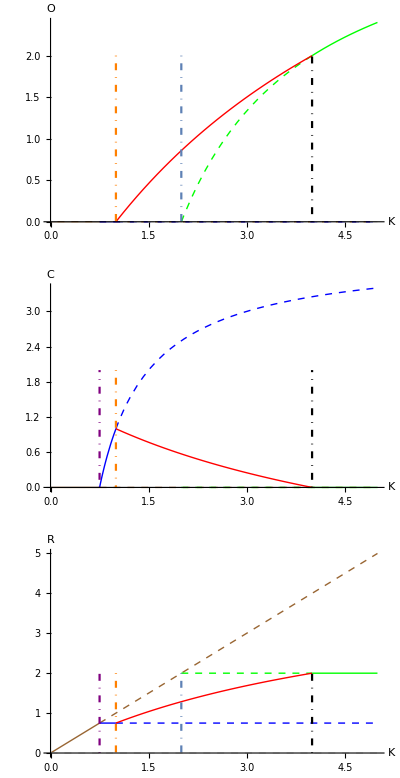

```mathematica
GraphicsGrid[{{
Show[PlotEqO1,PlotEqO1u,  PlotEqO2,PlotEqO2u,  PlotEqO3,PlotEqO3u,  PlotEqO4,PlotEqO4u,  PlotEqO5,PlotEqO5u, PlotEqO6,PlotEqO6u,
pRstarO,pRCstarO,pCex,
PlotRange->Automatic,AxesLabel->{"K","O"}]
},{
Show[PlotEqC1,PlotEqC1u,  PlotEqC2,PlotEqC2u,  PlotEqC3,PlotEqC3u,  PlotEqC4,PlotEqC4u,  PlotEqC5,PlotEqC5u, PlotEqC6,PlotEqC6u,
pRstarC,pRCstarO,pCex,
PlotRange->Automatic,AxesLabel->{"K","C"}]
},{
Show[PlotEqR1,PlotEqR1u,  PlotEqR2,PlotEqR2u,  PlotEqR3,PlotEqR3u,  PlotEqR4,PlotEqR4u,  PlotEqR5,PlotEqR5u, PlotEqR6,PlotEqR6u,
pRstarC,pRstarO,pRCstarO,pCex,
PlotRange->Automatic,AxesLabel->{"K","R"}]
}}]
```

```mathematica
(* Simulate dynamics *)
dR=R'[t]== r R[t](1-R[t]/Κ) -aRC R[t] Χ[t] - aRO R[t] Ω[t];
dC=Χ'[t]==  eRC aRC R[t] Χ[t] -  aCO Χ[t] Ω[t] - mC Χ[t];
dO=Ω'[t]==  eRO aRO R[t] Ω[t]+ eCO aCO Χ[t] Ω[t] - mO Ω[t];

init={ R[0]==0.01, Χ[0]==0.01, Ω[0]==0.01};
LineCols={{Thick,Green},{Thick,Blue},{Thick,Red}};
```

```mathematica
Manipulate[
dyn=NDSolve[{{dR,dC,dO}/.subparms/.Κ->k,init}, {R[t], Χ[t], Ω[t]}, {t,0,Tmax}];

Plot[Evaluate[{R[t], Χ[t], Ω[t]}/.dyn], {t,0,Tmax},PlotStyle->LineCols],

{{k,3,"K"},0.1,6},
{{Tmax,1000},100,1000}]
```